# La triangulation

## La théorie

Le présent document vise à illustrer le principe de triangulation, tel que vu en classe, pour les problèmes à deux dimension.

On commence par définir trois points de coordonnées connues, qui seront nos trois repères.

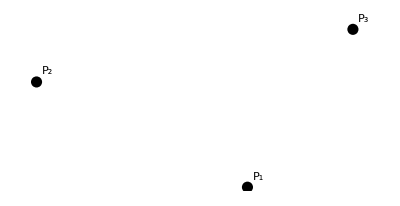

```mathematica
Subscript[P, 1]={0, 0}; Subscript[P, 2]={-4, 2}; Subscript[P, 3]={2, 3};
Table[{Subscript[x, i], Subscript[y, i]}=Subscript[P, i], {i, 1, 3}];
(* Ce code affiche les trois points de repère *)
Show[
graphicsP=Table[
Graphics[
{PointSize[.02],Point[Subscript[P, i]], Text[Unevaluated[Subscript[P, #]]&@i, Subscript[P, i]+{.2, .2}]}],
{i, 1, 3}
]
]
```

On imagine qu’on se trouve à une position inconnue. Ici, nous allons simuler cela en choisissant une position aléatoire X, mais nous essayerons ensuite de la retrouver « sans tricher ».

Pour des raisons que nous verrons plus loin, on va se limiter à une précision au millième d’unités, et on va tout conserver sous forme d’entiers pour que Mathematica puisse faire les calculs sous forme symbolique et conserver une précision infinie.

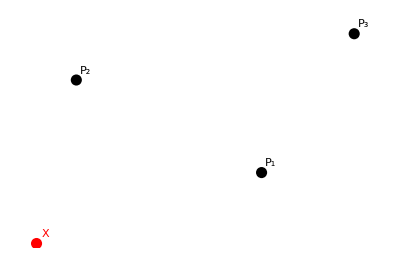

```mathematica
X=1/1000 RandomInteger[{-5000, 5000}, 2];
Show[
graphicsP,
graphicsX=Graphics[{Red, PointSize[.02], Point[X],
Text[Unevaluated[X], X + {.2, .2}]}],
PlotRange->All
]
```

Pour trianguler la position de X, on assume qu’on connaît les distances  des points P_1, P_1, P_3 à notre point X inconnu :

```mathematica
Table[Subscript[r, i]=Norm[X-Subscript[P, i]], {i, 1, 3}];
Print["r_1 = ",Subscript[r, 1]];Print["r_2 = ",Subscript[r, 2]];Print["r_3 = ",Subscript[r, 3]];
```

r_1 = (√(2595997/10))/100

r_2 = (√(1321997/10))/100

r_3 = (√(6759397/10))/100

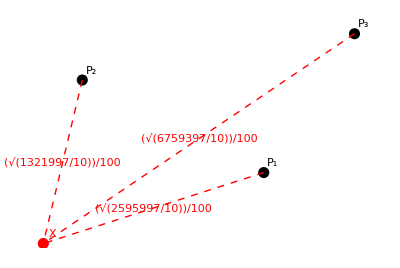

```mathematica
(* Ce code dessine les lignes droites et montre les distances sur le graphique. *)
Show[graphicsP, graphicsX,
graphicsLines=Table[
Graphics[
{Red, Dashed, Line[{Subscript[P, i], X}],
Text[Subscript[r, i], Mean[{Subscript[P, i], X}]]}
],
{i, 1, 3}
]
]
```

On said que notre point X={x, y} est une solution du système d’équations non-linéaires suivant :

```mathematica
sysEq=Table[
Subscript[r, i]^2==(x-Subscript[x, i])^2+(y-Subscript[y, i])^2,
{i, 1, 3}]
```

{2595997/100000==x^2+y^2,1321997/100000==(4+x)^2+(-2+y)^2,6759397/100000==(-2+x)^2+(-3+y)^2}

```mathematica
{554669/40000==x^2+y^2,2088909/40000==(4+x)^2+(-2+y)^2,1890589/40000==(-2+x)^2+(-3+y)^2}
```

{554669/40000==x^2+y^2,2088909/40000==(4+x)^2+(-2+y)^2,1890589/40000==(-2+x)^2+(-3+y)^2}

On peut donc trouver le point X en solutionnant ce système :

```mathematica
sol=Solve[sysEq, {x, y}]
```

{{x→-4859/1000,y→-1533/1000}}

On peut comparer avec le point X initialement choisi :

```mathematica
Print["X = ", X];
Print[" ( = ", N@X, ")"];
```

X = {-4859/1000,-1533/1000}

( = {-4.859,-1.533})

## En pratique

On remarque qu’on a du choisir un point aléatoire au millième près, afin de préserver une précision infinie dans les calculs avec Mathematica. En pratique, par contre, les données dont on dispose ne seront pas infiniment précises, et il faudra se permettre des approximations.

On refait ici le même procédé de triangulation, mais avec des distances « imprécises ».

```mathematica
(* Coordonnées des points de repère, connus *)
Subscript[P, 1]={0, 0};Subscript[P, 2]={-4, 2}; Subscript[P, 3]={2, 3};
Table[{Subscript[x, i], Subscript[y, i]}=Subscript[P, i], {i, 1, 3}];
Print["Repères : "];
Print["P_1 = ", Subscript[P, 1]];
Print["P_2 = ", Subscript[P, 2]];
Print["P_3 = ", Subscript[P, 3]];

(* Point que l'on désire trianguler *)
X=N@X+RandomReal[{-.0005, .0005},2]; (* On ajoute une petite perturbation aléatoire au point inconnu *) 

(* Distances *)
Table[Subscript[r, i]=Norm[X-Subscript[P, i]], {i, 1, 3}];
Print["\nDistances : "];
Print["r_1 = ", Subscript[r, 1]];
Print["r_2 = ", Subscript[r, 2]];
Print["r_3 = ", Subscript[r, 3]];

(* Le système d'équations *)
Print["\nSystème d'équations : "];
sysEq=Table[
Subscript[r, i]^2==(x-Subscript[x, i])^2+(y-Subscript[y, i])^2,
{i, 1, 3}
]

Print["Solutions : "];
Solve[sysEq, {x, y}]
```

Repères :

P_1 = {0,0}

P_2 = {-4,2}

P_3 = {2,3}

Distances :

r_1 = 5.09495

r_2 = 3.63618

r_3 = 8.22152

Système d'équations :

{25.9585==x^2+y^2,13.2218==(4+x)^2+(-2+y)^2,67.5934==(-2+x)^2+(-3+y)^2}

Solutions :

{}

On remarque que l’ensemble des solutions est vide! Pourquoi?
C’est parce qu’on cherche le point de triple-intersection de trois cercles  :

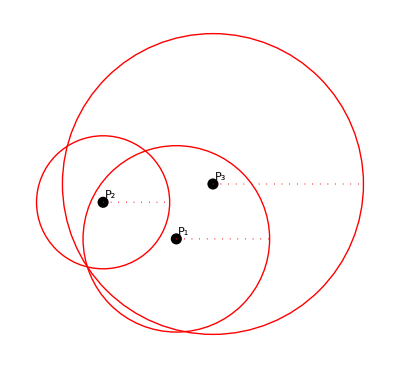

```mathematica
Show[
graphicsP=Table[
Graphics[
{PointSize[.02],Point[Subscript[P, i]], Text[Unevaluated[Subscript[P, #]]&@i, Subscript[P, i]+{.4, .4}]}],
{i, 1, 3}
],

graphicsL=Table[
Graphics[
{Red, Dotted, Line[{Subscript[P, i], Subscript[P, i]+{Subscript[r, i], 0}}]}
],
{i, 1, 3}],
graphicsC = Table[
Graphics[
{Red, Circle[Subscript[P, i], Subscript[r, i]]}
],
{i, 1, 3}
]
]
```

Or, avec des données de triangulation non parfaitement précises, il se peut très bien que les trois cercles ne se coupent pas exactement tous en un seul point. Par exemple, ici, si on zoom, on voit :

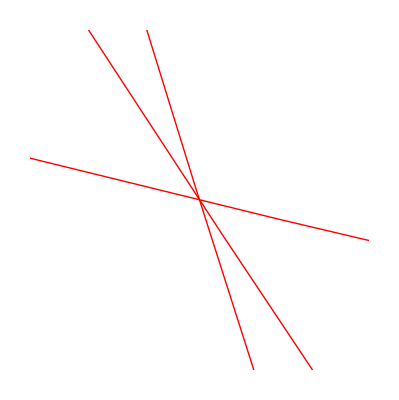

```mathematica
(* On affiche le même dessin, mais on zoom autour des points d'intersection des cercles. *)
Show[graphicsP, graphicsL, graphicsC,
PlotRange->{{X[[1]]-.02, X[[1]]+.02}, {X[[2]]-.02, X[[2]]+.02}}]
```

C’est la raison pour laquelle on ne trouve pas de solution à notre système à trois équations...

La meilleure façon de régler notre problème, pour s’assurer de trouver une solution c’est

On commence par solutionner un système de deux des trois équations;

Ce système devrait donner deux solutions; on choisit ensuite celle des deux qui est la plus proche d’être la bonne, en vérifiant la distance au troisième point.

On résout le système d'équations :

{25.9585==x^2+y^2,13.2218==(4+x)^2+(-2+y)^2}

Les solutions possibles sont :

Solution 1 : {-4.85875,-1.53332}

Distance au point 3 : 8.22152

Solution 2 : {-1.68859,4.80699}

Distance au point 3 : 4.10743

La distance r_3 = 8.22152

Donc, on retient la solution 1 :

{-4.85875,-1.53332}

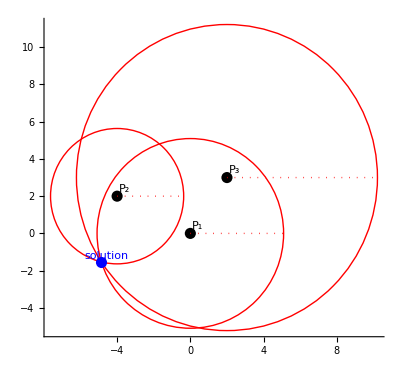

```mathematica
(* Le système d'équations à solutionner : *)
Print["On résout le système d'équations : "];
sysEq2=sysEq[[{1, 2}]]

(* La fonction NSolve résout le système numériquement; il y a deux solutions possibles, et on les stocke dans une liste : xPoss *)
xPoss={x, y}/.NSolve[sysEq2, {x, y}];
Print["\nLes solutions possibles sont :"];
Print["Solution 1 : ", xPoss[[1]]];
Print["\tDistance au point 3 : ", r13=Norm[Subscript[P, 3]-xPoss[[1]]]];
Print["Solution 2 : ", xPoss[[2]]];
Print["\tDistance au point 3 : ",
r23=Norm[Subscript[P, 3]-xPoss[[2]]]];

(* On choisit la solution dont la distance correspond le mieux *)
Print["\nLa distance r_3 = ", Subscript[r, 3]];
Print["Donc, on retient la solution ",
choix =If[Abs[Subscript[r, 3]-r13]<Abs[Subscript[r, 3]-r23], 
1, 2], " : "];
Print[xPoss[[choix]]];

Show[graphicsP, graphicsL, graphicsC, 
graphicsSol = Graphics[
{Blue, PointSize[.02], Point[xPoss[[choix]]],
Text["solution", xPoss[[choix]]+{.3, .3}]
}
],
Axes->True
]
```

La solution ainsi retrouvée ne sera pas « exactement » le point initial, mais on en sera suffisamment près :

```mathematica
Norm[X- xPoss[[choix]]]
```

9.15513×10^-16

## Une autre méthode

On peut également solutionner le problème en utilisant, même dans Mathematica, le truc vu en classe, soit de soustraire les équations l’une de l’autre. On fait par exemple :

```mathematica
Print["Système d'équations original : "];
sysEq = Table[Subscript[eq, i]=(Subscript[r, i]^2==(x-Subscript[x, i])^2+(y-Subscript[y, i])^2), {i, 1, 3}]

(* Soustraire des équations est compliqué, il faut convertir les équations en listes, puis les reconvertir en équations.
ici, l'équation linéaire i est Subscript[eq, i] - Subscript[eq, 3] *)
Print[" Système d'équations linéaire équivalent : "];
sysEqLin=Table[
Subscript[eqLin, i]=FullSimplify[Equal@@(List@@Subscript[eq, i]-List@@Subscript[eq, 3])],
{i, 1, 2}
]
```

Système d'équations original :

{25.9585==x^2+y^2,13.2218==(4+x)^2+(-2+y)^2,67.5934==(-2+x)^2+(-3+y)^2}

Système d'équations linéaire équivalent :

{28.6349+4 x+6 y==0,7+12 x+2 y==-54.3716}

Avec nos trois cercles, on obtient deux équations affines qui donneront une unique solution :

```mathematica
Print["Solution du système d'équations linéaire : "];
xSolLin={x, y}/.NSolve[sysEqLin, {x, y}]

Print["\nSolution avec les cercles : "];
xPoss[[choix]]

Print["\nDistance entre les deux : "];
Norm[xPoss[[choix]]-xSolLin[[1]]]
```

Solution du système d'équations linéaire :

{{-4.85875,-1.53332}}

Solution avec les cercles :

{-4.85875,-1.53332}

Distance entre les deux :

2.67377×10^-15